# HW3 Machine Learning for dataset 2 tornadoes

## Preprocessing

## Import the data set

```mathematica
resource = ResourceObject["Tornadoes in the U.S., 1950-2015"];
dataRaw = ResourceData[resource]
```

Dataset[<>]

This data set contains mixed types of data. The aim is is to classify each tornadoes into different magnitude.

## Explore the data set

### Scale measure system

```mathematica
scales = Sort[Union @ dataRaw[[All, "Magnitude"]]]
```

Dataset[<>]

These magnitude are measured in two different scale.

```mathematica
{Select[scales,StringMatchQ[#,"EF*"]&],Select[scales,StringMatchQ[#,"F*"]&]}
```

{Dataset[<>],Dataset[<>]}

-Graphics-

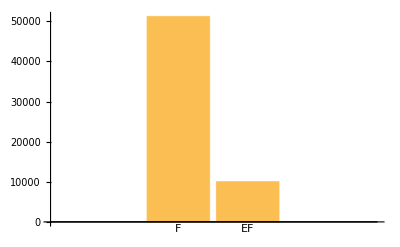

```mathematica
dis = Sort[Tally[dataRaw[[All, "Magnitude"]]]];
fCount= Select[dis,StringMatchQ[#[[1]],"F*"]&];
efCount= Select[dis,StringMatchQ[#[[1]],"EF*"]&];
PieChart[{Normal[fCount[All,2]], Normal[efCount[All,2]]}, ChartLegends->Normal[fCount[All,1]]]
BarChart[{Total[fCount[All,2]], Total[efCount[All,2]]},ChartLabels->{"F","EF"}]
```

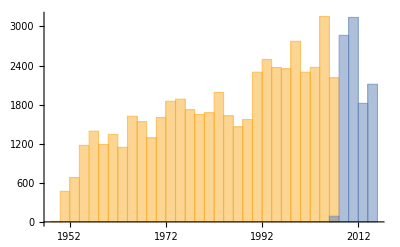

```mathematica
DateHistogram[{Select[dataRaw,StringMatchQ[#["Magnitude"],"F*"]&][[All,"Date"]],Select[dataRaw,StringMatchQ[#["Magnitude"],"EF*"]&][[All,"Date"]]}]
```

EF seems to count more tornadoes into smaller scale, so F0 has higher percentage. So the map from F to EF is not linear transform. EF are recently used to measure the tornadoes. F scale have more data than EF scale. It is better to extract F scale data for training the classifier.

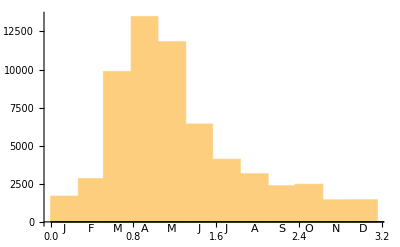

```mathematica
DateHistogram[dataRaw[[All,"Date"]],"Month",DateReduction->"Year"]
```

It seems tornadoes are more likely to happen during the Match and May.

### Position

```mathematica
GeoRegionValuePlot[Rule@@@Tally[dataRaw[All, "Location"]], GeoRange -> LinguisticAssistant]
```

-Graphics-

```mathematica
GeoHistogram[dataRaw[[All,"Start"]],GeoRange -> LinguisticAssistant]
```

-Graphics-

Tornadoes are strongly related to position.

## Extract the data with Fujita scale

```mathematica
data = Select[dataRaw,MemberQ[{"F0", "F1", "F2", "F3", "F4", "F5"},#["Magnitude"]]&]
```

Dataset[<>]

## Transform the date into year, month, hour

This is for training in random forest. Because if we train the data set directly, the random forest classifier takes too long time for training.

```mathematica
DateObject[{1950,1,31,12,6,10.},"Instant","Gregorian","America/Chicago"][{"Year", "Month","Hour"}]
```

{1950,1,12}

```mathematica
timeData = Append[#, {"Year"-> #[["Date"]]["Year"],"Month"-> #[["Date"]]["Month"],"Hour"-> #[["Date"]]["Hour"]}]& /@ data[[All]];
timeData =timeData[[All,Normal[Keys[timeData[[1]]]/."Date"-> Nothing]]]
```

Dataset[<>]

## Transform the interval data into min, max, mean

```mathematica
Min[Quantity[Interval[{50000,500000}], "USDollars"]]
Max[Quantity[Interval[{50000,500000}], "USDollars"]]
Mean[{Min[#],Max[#]}]&[Quantity[Interval[{50000,500000}], "USDollars"]]
```

50000 $

500000 $

275000 $

```mathematica
intData = Append[#, "EstimatedPropertyLoss_Min" -> Min[#[["EstimatedPropertyLoss"]]]]& /@ timeData[[All]];
intData = Append[#, "EstimatedPropertyLoss_Max" -> Max[#[["EstimatedPropertyLoss"]]]]& /@ intData[[All]];
intData = Append[#, "EstimatedPropertyLoss_Mean" -> Mean[#[[{"EstimatedPropertyLoss_Min", "EstimatedPropertyLoss_Max"}]]]]& /@ intData[[All]];
intData =intData[[All,Normal[Keys[intData[[1]]]/."EstimatedPropertyLoss"-> Nothing]]]
```

Dataset[<>]

## Transform the location data into geo position

```mathematica
Interpreter["Location"][Entity["AdministrativeDivision",{"Texas","UnitedStates"}]]
```

GeoPosition[{31.4818,-99.3701}]

```mathematica
geoData = Append[#, "LocationGeo" -> Interpreter["Location"][#[["Location"]]]]& /@ intData[[All]];
processedData =geoData[[All,Normal[Keys[geoData[[1]]]/."Location"-> Nothing]]]
```

Dataset[<>]

## Save the processed data for later use

```mathematica
Export["processed.mx", processedData]
```

processed.mx

```mathematica
processedData = Import["processed.mx"]
```

Dataset[<>]

## Set up the feature and target data association

```mathematica
Features = Select[Normal[Keys[processedData[[1]]]], !MemberQ[{"Magnitude"}, #] &]
Target = "Magnitude";
```

{Number,StateNumber,Injuries,Fatalities,EstimatedCropLoss,Start,End,MagnitudeEstimatedQ,Year,Month,Hour,EstimatedPropertyLoss_Min,EstimatedPropertyLoss_Max,EstimatedPropertyLoss_Mean,LocationGeo}

```mathematica
Length[Features]
```

15

Totally, we have 15 features.

```mathematica
featureData  = processedData[All,Features];
targetData = processedData[All,Target];
linkedData = Thread[Normal[Values[featureData]] -> Normal[targetData]]
```

{{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.83,-90.03}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.82,-90.12}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,51189,{1098,198,0,0 people,Missing[NotAvailable],GeoPosition[{33.42,-101.62}],GeoPosition[{33.42,-101.6}],False,2007,11,3,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],GeoPosition[{31.4818,-99.3701}]}→F0}
 |  |  |  |

## Split the train and test data

```mathematica
trainData = Drop[linkedData,{1,-1,5}]
testData = Take[linkedData,{1,-1,5}]
```

{{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.82,-90.12}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,40952}
 |  |  |  |

{{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.83,-90.03}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,10238}
 |  |  |  |

### save the train and test data for later

```mathematica
Export["trainData.mx", trainData];
Export["testData.mx", testData];
```

```mathematica
trainData = Import["trainData.mx"]
testData = Import["testData.mx"]
```

{{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.82,-90.12}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,40952}
 |  |  |  |

{{1,1,3,0 people,Missing[NotAvailable],GeoPosition[{38.77,-90.22}],GeoPosition[{38.83,-90.03}],False,1949,12,3,500000 $,5000000 $,2750000 $,GeoPosition[{38.3735,-92.4735}]}→F3,10238}
 |  |  |  |

## Classify the data set

## Neural Network

```mathematica
c=Classify[trainData,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c,"TrainingTime"]
```

630.536 s

### Save the classifier for later

```mathematica
Export["NN_classifier.mx",c]
```

NN_classifier.mx

```mathematica
c = Import["NN_classifier.mx"]
```

ClassifierFunction[…]

### Measure the performance of the classifier

```mathematica
cm = ClassifierMeasurements[c,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.625354

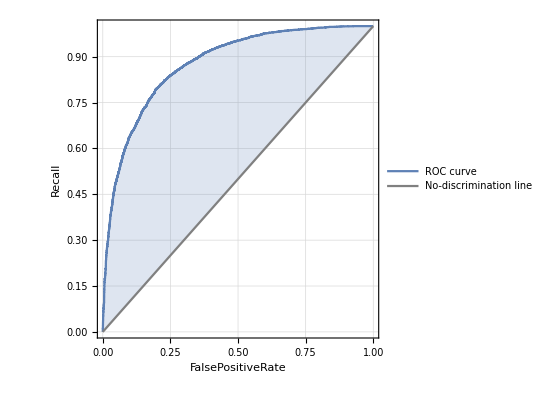
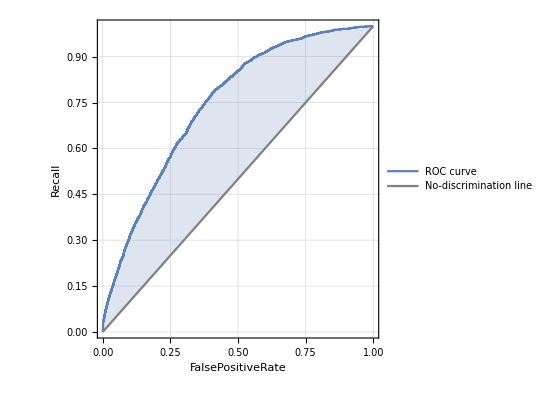
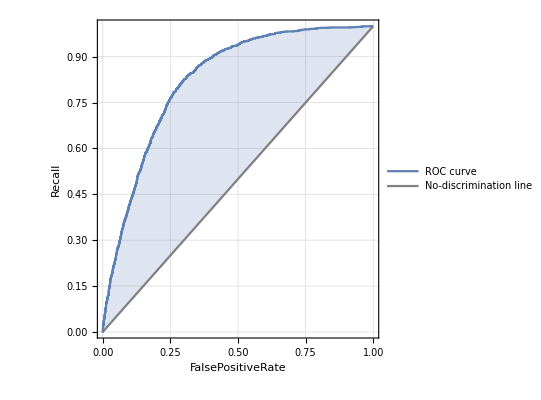
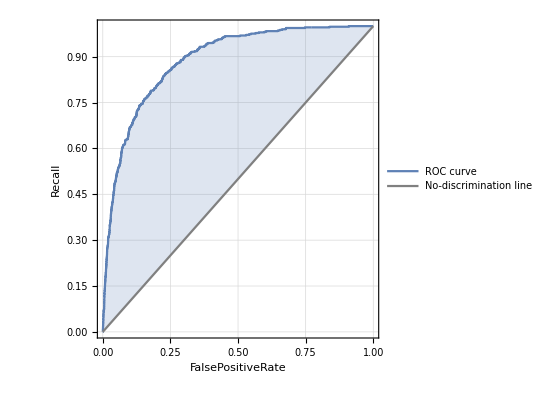
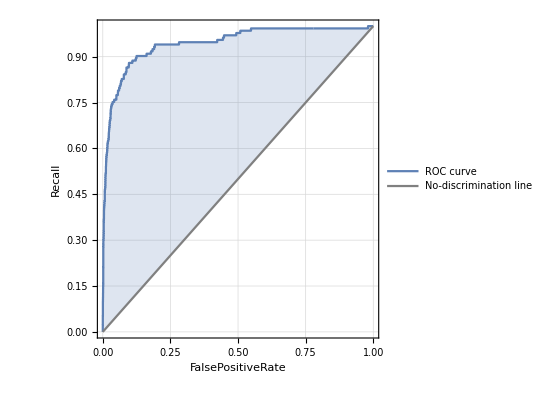
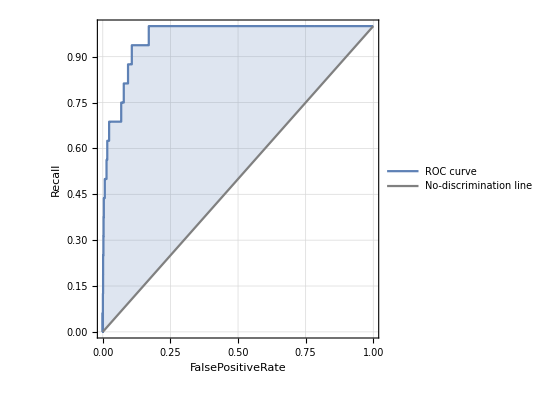
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
cm/@{"ROCCurve"}//TableForm
```

```mathematica
cm["Recall"]
```

<|F0→0.776252,F1→0.620373,F2→0.358079,F3→0.254098,F4→0.278195,F5→0.125|>

```mathematica
cm["Precision"]
```

<|F0→0.764065,F1→0.535149,F2→0.454834,F3→0.447653,F4→0.578125,F5→0.2|>

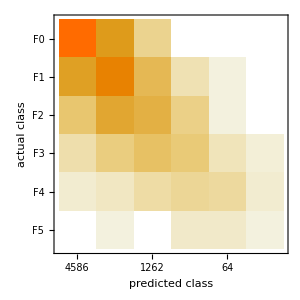

```mathematica
cm["ConfusionMatrixPlot"]
```

## Random Forest

```mathematica
crf=Classify[trainData,Method->"RandomForest"]
```

ClassifierFunction[…]

### Save the classifier

```mathematica
Export["RF_Classifier.mx",crf]
```

RF_Classifier.mx

```mathematica
crf= Import["RF_Classifier.mx"]
```

ClassifierFunction[…]

### Measure the performance of the classifier

```mathematica
ClassifierInformation[crf,"TrainingTime"]
```

643.065 s

```mathematica
crfm = ClassifierMeasurements[crf,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
crfm["Accuracy"]
```

0.670671

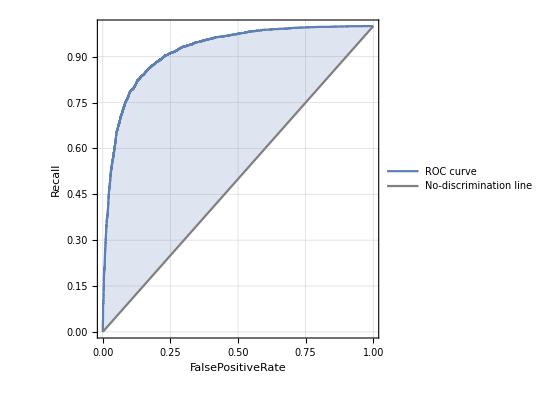
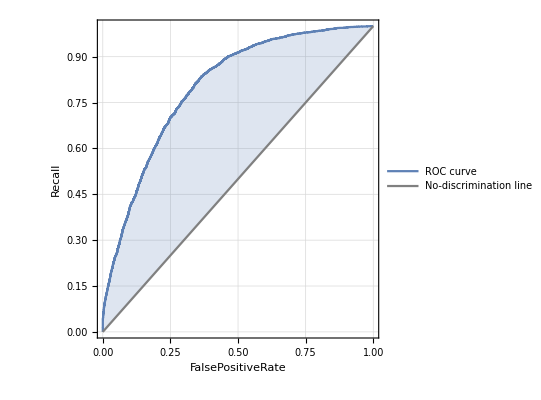
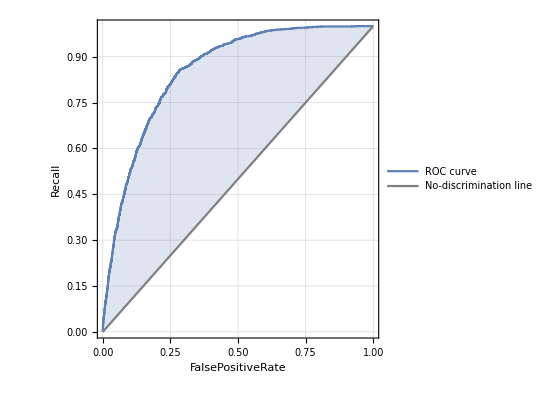
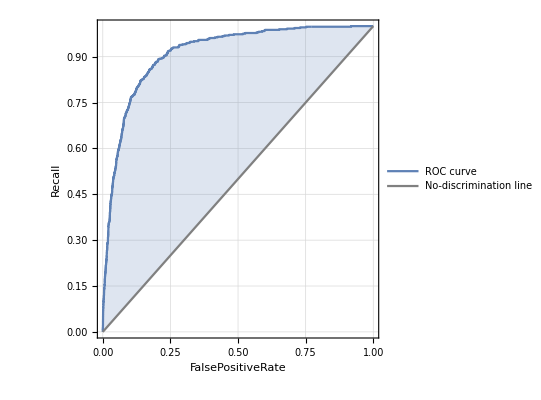
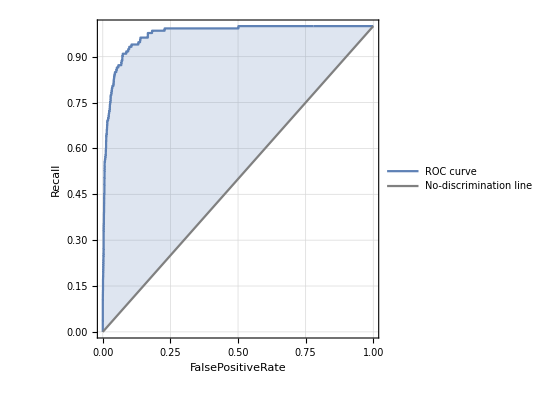
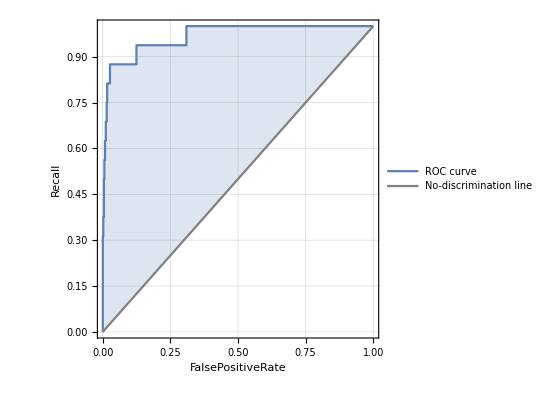
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
crfm/@{"ROCCurve"}//TableForm
```

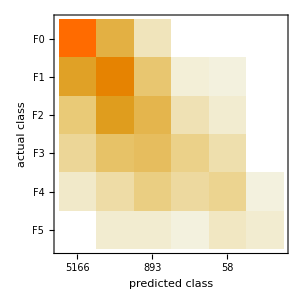

```mathematica
crfm["ConfusionMatrixPlot"]
```

```mathematica
crfm["Recall"]
```

<|F0→0.885467,F1→0.668293,F2→0.280724,F3→0.108607,F4→0.263158,F5→0.1875|>

```mathematica
crfm["Precision"]
```

<|F0→0.773713,F1→0.578203,F2→0.503919,F3→0.588889,F4→0.603448,F5→0.75|>

## K-Nearest Neighbors

```mathematica
cknn=Classify[trainData,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

### Save the classifier for later

```mathematica
Export["knn_Claasifier.mx",cknn]
```

knn_Claasifier.mx

```mathematica
cknn = Import["knn_Claasifier.mx"]
```

ClassifierFunction[…]

### Measure the performance of the classifier

```mathematica
ClassifierInformation[cknn,"TrainingTime"]
```

652.787 s

```mathematica
cknnm = ClassifierMeasurements[cknn,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cknnm["Accuracy"]
```

0.552984

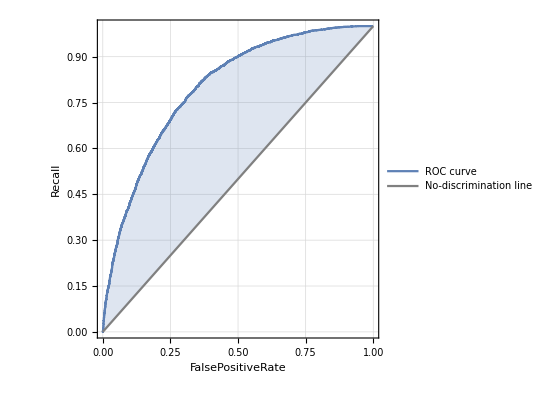
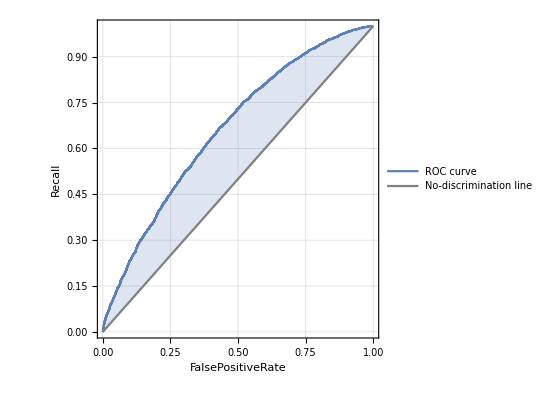
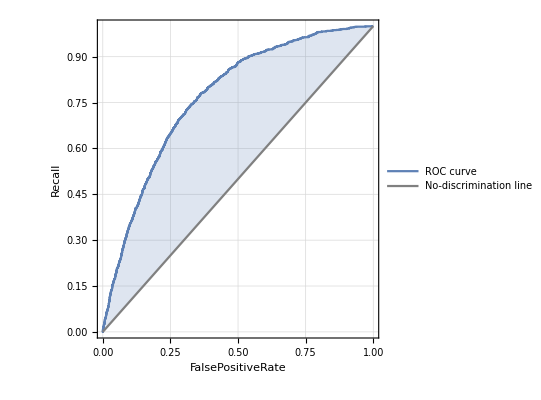
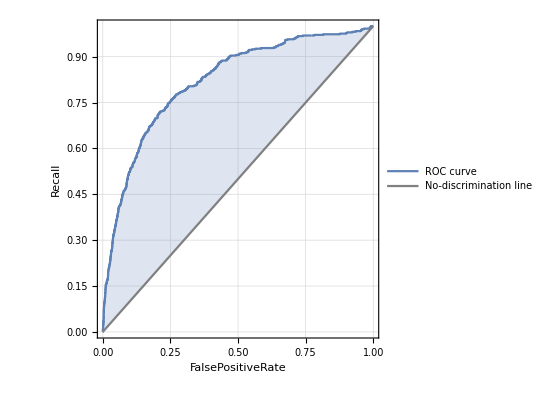
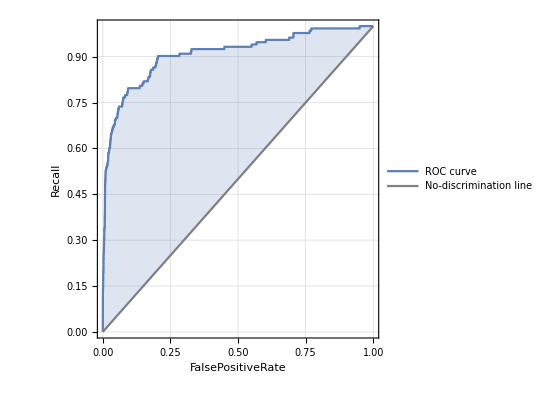
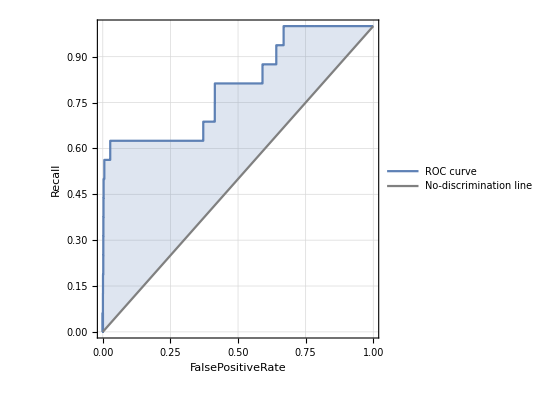
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
cknnm/@{"ROCCurve"}//TableForm
```

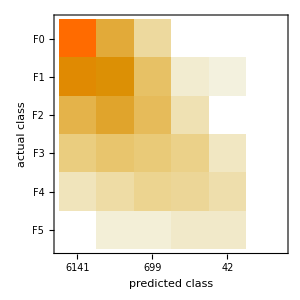

```mathematica
cknnm["ConfusionMatrixPlot"]
```

```mathematica
cknnm["Recall"]
```

<|F0→0.838946,F1→0.43472,F2→0.181535,F3→0.0901639,F4→0.18797,F5→0.|>

```mathematica
cknnm["Precision"]
```

<|F0→0.616675,F1→0.465581,F2→0.416309,F3→0.427184,F4→0.595238,F5→Indeterminate|>

## Comparison & conclusion

## Training time

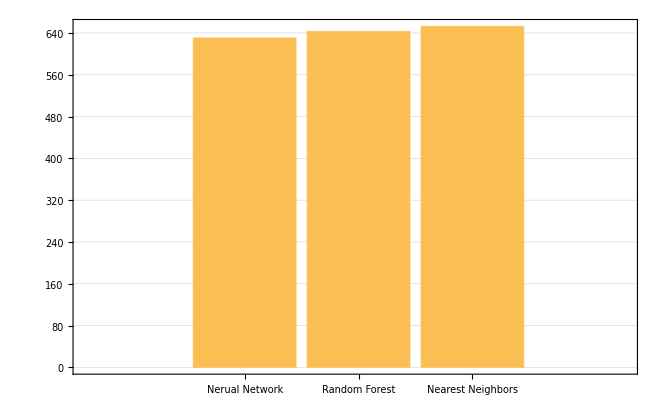

```mathematica
BarChart[{ClassifierInformation[c,"TrainingTime"], ClassifierInformation[crf,"TrainingTime"], ClassifierInformation[cknn,"TrainingTime"]}, ChartLabels->{"Nerual Network", "Random Forest", "Nearest Neighbors"}, PlotTheme->"Detailed"]
```

Three of the methods have approximately the same training time. 10-11mins for training.

## Accuracy

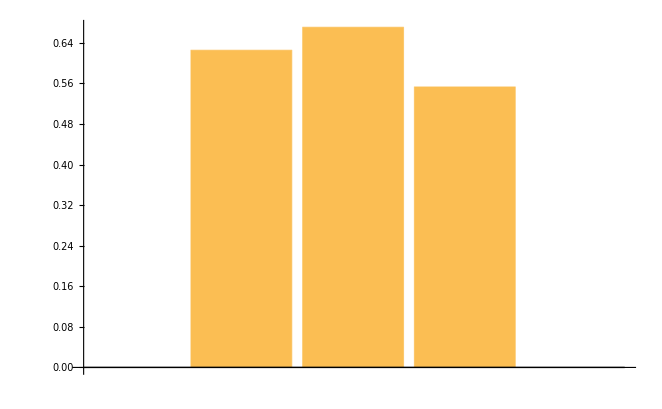

```mathematica
BarChart[{cm["Accuracy"], crfm["Accuracy"],cknnm["Accuracy"]}]
```

Random Forest has the highest accuracy and then the Neural Network. Both of them are over 60%. However, the Nearest Neighbor is not good as the previously two, it only has 55%.

## Precision

```mathematica
Dataset[{Append[<|"Method"-> "Neural Network"|>,cm["Precision"]],
Append[<|"Method"-> "Random Forest"|>,crfm["Precision"]],
Append[<|"Method"-> "k Nearest Neighbors"|>,cknnm["Precision"]]}]
```

Dataset[<>]

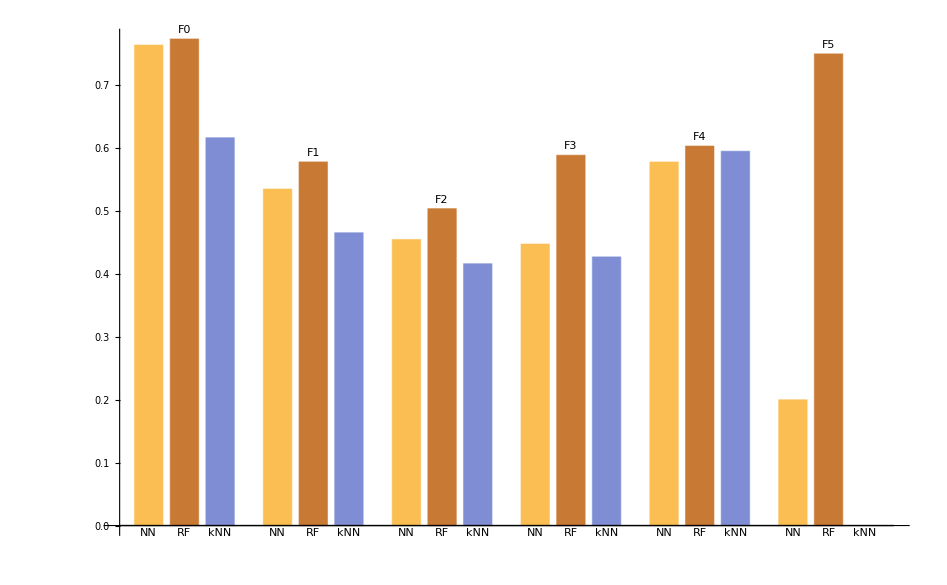

```mathematica
BarChart[{Values[cm["Precision"]][[#]],Values[crfm["Precision"]][[#]],Values[cknnm["Precision"]][[#]]}&/@Range[Length[cm["Precision"]]],ChartLabels->{Placed[Keys[cm["Precision"]],Above],{"NN", "RF","kNN"}}]
```

As we can see from the bar chart, Random Forest shows the best of the three in every classes. Then the Neural Network. kNN has the worst performance.

## Recall

```mathematica
Dataset[{Append[<|"Method"-> "Neural Network"|>,cm["Recall"]],
Append[<|"Method"-> "Random Forest"|>,crfm["Recall"]],
Append[<|"Method"-> "k Nearest Neighbors"|>,cknnm["Recall"]]}]
```

Dataset[<>]

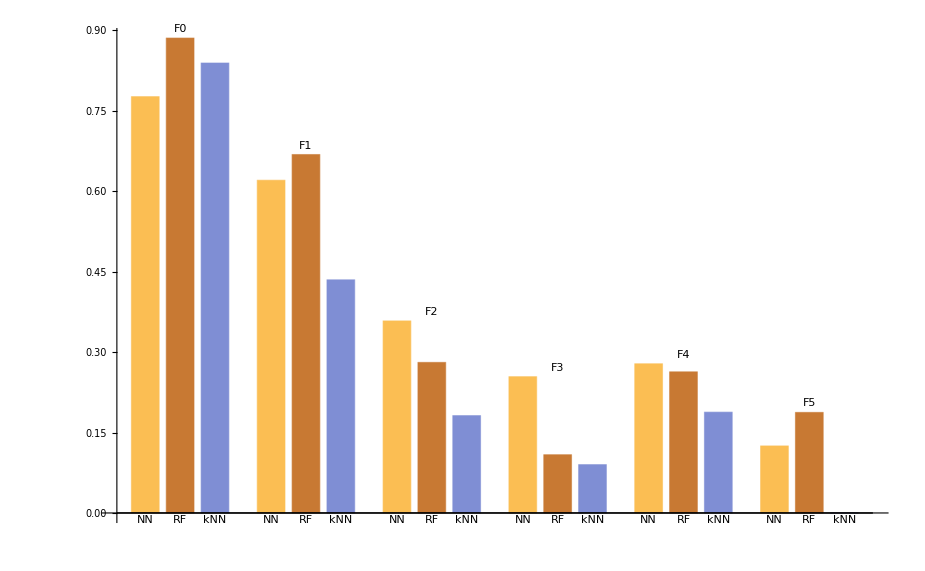

```mathematica
BarChart[{Values[cm["Recall"]][[#]],Values[crfm["Recall"]][[#]],Values[cknnm["Recall"]][[#]]}&/@Range[Length[cm["Precision"]]],ChartLabels->{Placed[Keys[cm["Precision"]],Above],{"NN", "RF","kNN"}}]
```

F0, F1 have higher recall rate than the rest. Random forest shows the best performance in these two and F5.
For F2, F3, F4 Neural Network has the best performance.
Again, the kNN has the worst performance.

## ROC Curve Comparison

```mathematica
ROCcmp[i_]:=Module[{},g1 = cm["ROCCurve"][i];
col1 = Cases[g1,_RGBColor,Infinity][[1]];
col11 = Cases[g1,_,Infinity][[-1]];
g1l = g1/.col11->Placed[,After,Identity];
g1c = g1l/.col1->Red;
g2 = crfm["ROCCurve"][i];
col2 = Cases[g2,_RGBColor,Infinity][[1]];
col21 = Cases[g2,_,Infinity][[-1]];
g2l = g2/.col21->Placed[,After,Identity];
g2c = g2l/.col2->Blue;
g3 = cknnm["ROCCurve"][i];
col3 = Cases[g3,_RGBColor,Infinity][[1]];
col31 = Cases[g3,_,Infinity][[-1]];
g3l = g3/.col31->Placed[,After,Identity];
g3c = g3l/.col3->Yellow;
Show[g1c,g2c,g3c]]
```

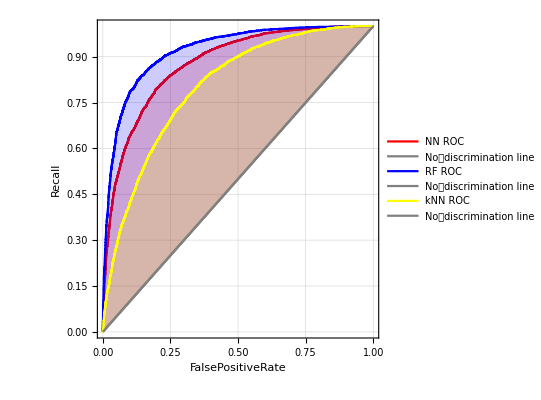

```mathematica
ROCcmp["F0"]
```

Random forest shows the best performance for F0

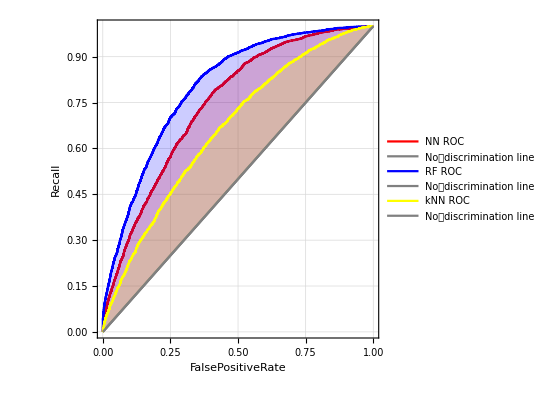

```mathematica
ROCcmp["F1"]
```

Random forest shows the best performance for F1

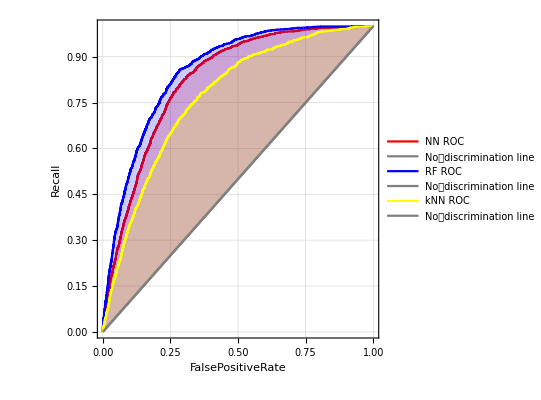

```mathematica
ROCcmp["F2"]
```

Random forest shows the best performance for F2

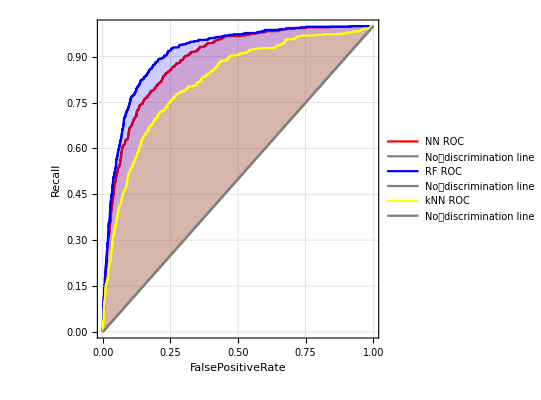

```mathematica
ROCcmp["F3"]
```

Random forest shows the best performance for F3

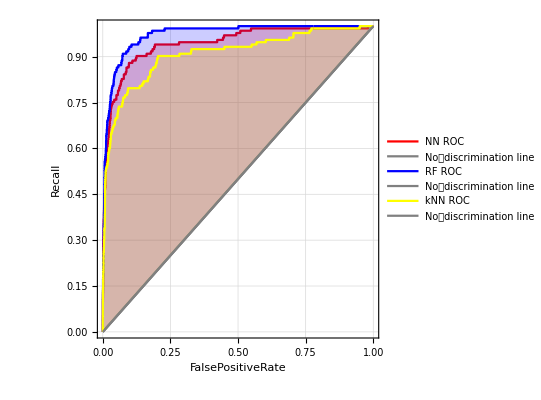

```mathematica
ROCcmp["F4"]
```

Random forest shows the best performance for F4

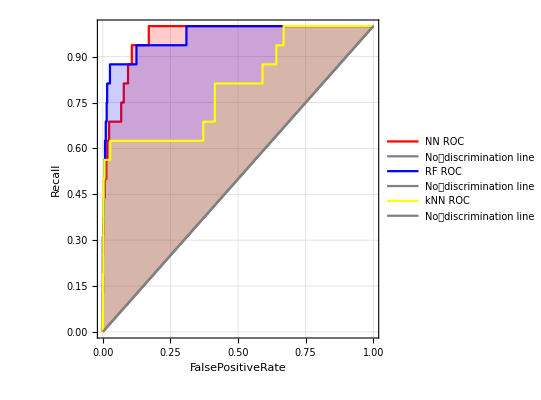

```mathematica
ROCcmp["F5"]
```

Random forest  and Neural Network both show the best performance for F5

## Confusion Matrix

```mathematica
d1 =cm["ConfusionMatrixPlot"];
d2 =crfm["ConfusionMatrixPlot"];
d3 =cknnm["ConfusionMatrixPlot"];
{"NN"-> d1,"RF"-> d2,"kNN"-> d3}
```

{NN→-Graphics-,RF→-Graphics-,kNN→-Graphics-}

The classifier is not good at classify F1 and F2. Lots of F2 has been classified into F1. The data is imbalanced and most of the data are concentrated in small scale.

## Conclusion

### Preprocessing

Due to the fact that most data are measured in Fujita Scale and there is no easy way to transform Fujita Scale to Enhanced Fujita Scale. I only use Fujita Scale data for training.
Transform the date Object into year, month, day will dramatically improve the speed of training.
The Location data need an interpreter in order to process it in Classifier. I interpret it as the GeoPosition.

### Training

Three methods including Neural Network, Random Forest, Nearest Neighbors are used to classify the data set. Training times are close about 10 to 11 minutes.

### Result

Random forest shows the best performance in terms of accuracy. Neural Network is also pretty good. Due to the fact that tornadoes are strongly related to location and season, i think it may be good to use the Nearest Neighbors to take several neighbor points together. However, the result is not good. The reason could be that some small tornadoes may happen right after a big one. The Nearest Neighbor just put them together and that is not matched with fact.